# IPPT Model

## 3. Single Case Solver

Instructions:
- This notebook will evaluate the model using a single set of input conditions

How to Run:
- Define the input conditions you desire
- Click “Evaluate Notebook in Menu Options”
- Only the time-to-solution will be output explicitly, use “3. Single Case Plots” to visualize model results

## Inputs

Notes:
- Inputs loaded from csv file with name “DataIO-Run#.csv”
- Evaluate first cell then click “Browse...” button below to find csv file

```mathematica
Clear[DataIOFile]
FileNameSetter[Dynamic[DataIOFile],"OpenList"]
```

$CellContext`DataIOFileOpenListAll

```mathematica
(** Evaluate this to load csv file data **)
MasterTable=Import[DataIOFile[[1]]];
Nsols=Dimensions[MasterTable][[1]]-1

(** Generate Tables of Data from MasterTable **)

zmaxT=MasterTable[[2;;Nsols+1,1]];
zstepsT=MasterTable[[2;;Nsols+1,2]];
tmaxT=MasterTable[[2;;Nsols+1,3]];
tstepsT=MasterTable[[2;;Nsols+1,4]];
zs0T=MasterTable[[2;;Nsols+1,5]];
ws0T=MasterTable[[2;;Nsols+1,6]];
nn0T=MasterTable[[2;;Nsols+1,7]];
χi0T=MasterTable[[2;;Nsols+1,8]];
zχiT=MasterTable[[2;;Nsols+1,9]];
Te0T=MasterTable[[2;;Nsols+1,10]];
Ti0T=MasterTable[[2;;Nsols+1,11]];
znT=MasterTable[[2;;Nsols+1,12]];
LcT=MasterTable[[2;;Nsols+1,13]];
L0T=MasterTable[[2;;Nsols+1,14]];
RcT=MasterTable[[2;;Nsols+1,15]];
C0T=MasterTable[[2;;Nsols+1,16]];
V0T=MasterTable[[2;;Nsols+1,17]];
zcT=MasterTable[[2;;Nsols+1,18]];
routT=MasterTable[[2;;Nsols+1,19]];
rinT=MasterTable[[2;;Nsols+1,20]];
zc0T=MasterTable[[2;;Nsols+1,21]];
vsfT=MasterTable[[2;;Nsols+1,22]];
wsfT=MasterTable[[2;;Nsols+1,23]];
nsfT=MasterTable[[2;;Nsols+1,24]];
TefT=MasterTable[[2;;Nsols+1,25]];
nffT=MasterTable[[2;;Nsols+1,26]];
vffT=MasterTable[[2;;Nsols+1,27]];
mbitT=MasterTable[[2;;Nsols+1,28]];
IbitT=MasterTable[[2;;Nsols+1,29]];
IspT=MasterTable[[2;;Nsols+1,30]];
ηTT=MasterTable[[2;;Nsols+1,31]];
ηTrecT=MasterTable[[2;;Nsols+1,32]];
ηmT=MasterTable[[2;;Nsols+1,33]];
MassFracT=MasterTable[[2;;Nsols+1,34]];
MassCheckT=MasterTable[[2;;Nsols+1,35]];
TdcT=MasterTable[[2;;Nsols+1,36]];
HeatParT=MasterTable[[2;;Nsols+1,37]];
(* ηerecT=MasterTable[[2;;Nsols+1,38]]; *)

(** Define physical parameters and funtions **)

ec=1.6 10^-19;    (* Electron Charge *)
me=9.11 10^-31;  (* Electron Mass *)
kb=1.38 10^-23;   (* Boltzmann Constant *)
g0=9.81;   (* Gravity *)
γ=5/3;      (* Polytropic Index *)   
μ0=4π 10^-7; 
ϵ0=8.85 10^-12;     (* Permeability of Free Space *)
AW=40;                               (* Atomic Weight *)
mi=AW 1.67 10^-27;      (* Ion Mass *)
un=((kb 298)/mi)^(1/2);             (* Neutral Sound Speed *)
Ses[Te_]:=2.336 10^-14 Te^1.609 Exp[0.0618 Log[Te]^2-0.1171 Log[Te]^3]; (* Ar electron-neutral scattering rate coef. in [m^3/s] for Te in [eV] *)
Sion[Te_]:= 2.34 10^-14 Te^0.59 Exp[-17.44/Te]; (* Ar electron-impact ionization rate coef. in [m^3/s] for Te in [eV] *)
Sexc[Te_]:=2.48 10^-14 Te^0.33 Exp[-12.78/Te]; (* Ar electron-neutral excitation rate coef. in [m^3/s] for Te in [eV] *)
ϵiz=15.76; (* ionization potential of Ar in [eV] *)
ϵex=12.14; (* first excitation potential of Ar in [eV] *)
ϵion[Te_]:=1/Sion[Te](Sion[Te]ϵiz+Sexc[Te]ϵex+Ses[Te](3me)/mi Te);       (* Ar effective ionization energy *)
σen=4 10^-20;   (* Ar ion-neutral cross-section, from Polzin J. Phys D, 2013 *)
σcx= 5 10^-19;    (* Ar charge-exchage cross-section, NEEDS UPDATED MODEL *)

Λ[ne_,Te_]:=Piecewise[{{23-Log[(ne 10^-6)^(1/2)Te^(-3/2)],Te<7.389},{24-Log[(ne 10^-6)^(1/2)Te^-1],Te≥7.389}}]    (* Coulomb Logarithm *)
νei[ne_,Te_]:=2.91 10^-12 ne Te^(-3/2)Λ[ne,Te]  (* e-i collision frequency *)
νen[nn_,Te_]:=nn σen ((8 ec Te)/(π me))^(1/2)    (*e-n collision frequency *)
ηcl[ne_,nn_,Te_]:=(me (νei[ne,Te]+νen[nn,Te]))/(ne ec^2)   (* Plasma Resistivity - Classical *)
δsd[Lterm_,Cp_,ne_,nn_,Te_]:=((2(ηcl[ne,nn,Te])(Lterm Cp)^(1/2))/μ0)^(1/2)   (* Skin Depth *)
Rp[Lterm_,Cp_,ne_,nn_,Te_,ws_,rout_,rin_]:=π (ηcl[ne,nn,Te])/Min[δsd[Lterm,Cp,ne,nn,Te],ws]((rout+rin)/(rout-rin))
Dp[ne_,nn_,Te_]:=Te/(ne ec ηcl[ne,nn,Te])(me/mi);

(** Create Tables of Other Relevant Parameters **)

ΠionT=Table[nn0T[[j]] χi0T[[j]] Sion[Te0T[[j]]] (L0T[[j]] C0T[[j]])^(1/2),{j,1,Nsols}];


Tdc=Table[zcT[[j]](mbitT[[j]]/(C0T[[j]] V0T[[j]]^2))^(1/2),{j,1,Nsols}];

TLC=Table[2π (LcT[[j]]C0T[[j]])^(1/2),{j,1,Nsols}];

TRL=Table[(LcT[[j]]/Rp[LcT[[j]],C0T[[j]],nn0T[[j]] ,nn0T[[j]],Te0T[[j]],ws0T[[j]],routT[[j]],rinT[[j]]]),{j,1,Nsols}];

fτ=Table[1-TLC[[j]]/(4π TdcT[[j]])Sin[4π(TdcT[[j]]/TLC[[j]])],{j,1,Nsols}];

EionT=Table[((1/2) C0T[[j]] V0T[[j]]^2)/(mbitT[[j]] (ec ϵion[Te0T[[j]]]/mi))Tdc[[j]]/TRL[[j]] fτ[[j]],{j,1,Nsols}];


(** Define Plot Styles **)

MultiCasePlot[Xtable_,Ytable_,xrange_,yrange_,xlabel_,ylabel_,join_]:=Show[{ListPlot[Table[{Xtable[[ii]],Ytable[[ii]]},{ii,1,Dimensions[Xtable][[1]]}],Joined->join,PlotStyle->Black,PlotRange->{xrange,yrange}]},
Frame->True,
ImageSize->330,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

LogLogMultiCasePlot[Xtable_,Ytable_,xrange_,yrange_,xlabel_,ylabel_,join_]:=Show[{ListLogLogPlot[Table[{Xtable[[ii]],Ytable[[ii]]},{ii,1,Dimensions[Xtable][[1]]}],Joined->join,PlotStyle->Black,PlotRange->{xrange,yrange}]},
Frame->True,
ImageSize->330,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

LogLinearMultiCasePlot[Xtable_,Ytable_,xrange_,yrange_,xlabel_,ylabel_,join_]:=Show[{ListLogLinearPlot[Table[{Xtable[[ii]],Ytable[[ii]]},{ii,1,Dimensions[Xtable][[1]]}],Joined->join,PlotStyle->Black,PlotRange->{xrange,yrange}]},
Frame->True,
ImageSize->330,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

LogLogContourPlot[X_,Y_,Z_,xlabel_,ylabel_,xmin_,xmax_,ymin_,ymax_]:=
Show[{
ListContourPlot[Table[{X[[j]],Y[[j]],Z[[j]]},{j,1,Nsols}],PlotRange->{{xmin,xmax},{ymin,ymax}},ColorFunction->({Opacity[0.5],ColorData["SandyTerrain"][#]}&),Method->{"TransparentPolygonMesh"->True},BaseStyle->Directive[Opacity[0.7]],ClippingStyle->False],
ListContourPlot[Table[{X[[j]],Y[[j]],Z[[j]]},{j,1,Nsols}],PlotRange->{{xmin,xmax},{ymin,ymax}},ContourShading->False,ContourStyle->{{Thickness[0.005],Black}},ClippingStyle->False]},
Frame->True,
ImageSize->330,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"},
FrameTicks->{
{{{-7,"10^-7"},
{Log[10,2 10^-7],"",{0.002,0}},
{Log[10,4 10^-7],"",{0.002,0}},
{Log[10,6 10^-7],"",{0.002,0}},
{Log[10,8 10^-7],"",{0.002,0}},
{-6,"10^-6"},
{Log[10,2 10^-6],"",{0.002,0}},
{Log[10,4 10^-6],"",{0.002,0}},
{Log[10,6 10^-6],"",{0.002,0}},
{Log[10,8 10^-6],"",{0.002,0}},
{-5,"10^-5"}},
{{-7,""},
{Log[10,2 10^-7],"",{0.002,0}},
{Log[10,4 10^-7],"",{0.002,0}},
{Log[10,6 10^-7],"",{0.002,0}},
{Log[10,8 10^-7],"",{0.002,0}},
{-6,""},
{Log[10,2 10^-6],"",{0.002,0}},
{Log[10,4 10^-6],"",{0.002,0}},
{Log[10,6 10^-6],"",{0.002,0}},
{Log[10,8 10^-6],"",{0.002,0}},
{-5,""}}},
{{{-2,"10^-2"},
{Log[10,2 10^-2],"",{0.002,0}},
{Log[10,4 10^-2],"",{0.002,0}},
{Log[10,6 10^-2],"",{0.002,0}},
{Log[10,8 10^-2],"",{0.002,0}},
{-1,"10^-1"},
{Log[10,2 10^-1],"",{0.002,0}},
{Log[10,4 10^-1],"",{0.002,0}},
{Log[10,6 10^-1],"",{0.002,0}},
{Log[10,8 10^-1],"",{0.002,0}},
{0,"1"}},
{{-2,""},
{Log[10,2 10^-2],"",{0.002,0}},
{Log[10,4 10^-2],"",{0.002,0}},
{Log[10,6 10^-2],"",{0.002,0}},
{Log[10,8 10^-2],"",{0.002,0}},
{-1,""},
{Log[10,2 10^-1],"",{0.002,0}},
{Log[10,4 10^-1],"",{0.002,0}},
{Log[10,6 10^-1],"",{0.002,0}},
{Log[10,8 10^-1],"",{0.002,0}},
{0,""}}}}]
```

220

## Single Plots

Notes:
-Plots a single variable X vs Y
-Generates a table of X and table of Y composed of different j solutions
-Not generally useful except for pattern finding

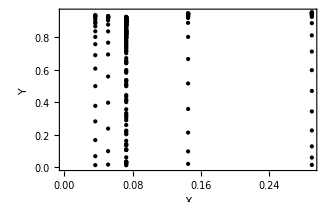

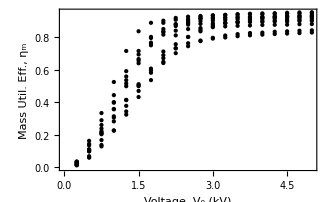

```mathematica
X=Table[ΠionT[[j]],{j,1,Nsols}];
Y=Table[ηmT[[j]],{j,1,Nsols}];
MultiCasePlot[X,Y,Automatic,Automatic,"X","Y",False]

MultiCasePlot[V0T/1000,ηmT,Automatic,Automatic,"Voltage, V_0 (kV)","Mass Util. Eff., η_m",False]
```

## Contour Plots

Notes:
-Generates contour plot of variable Z vs. X and Y
-Generates a table of X and table of Y composed of different j solutions
-Useful for paper plots of performance

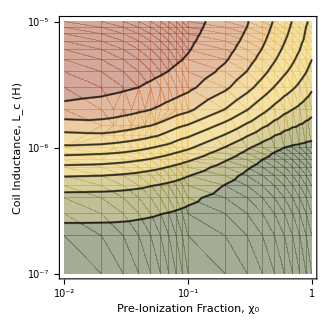

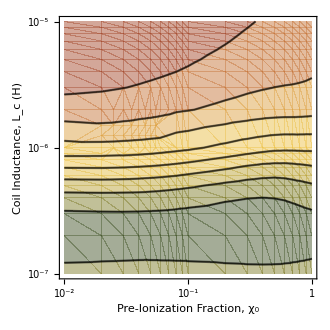

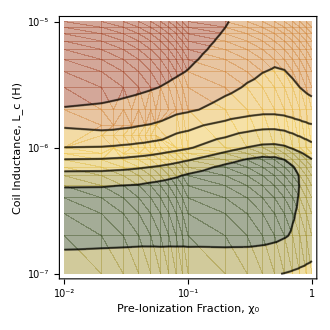

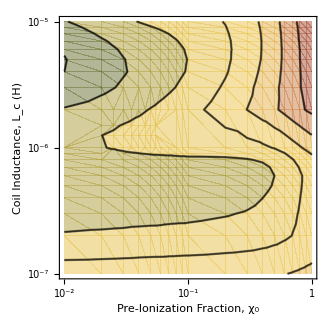

```mathematica
X=Table[Log[10,χi0T[[j]]],{j,1,Nsols}];
Y=Table[Log[10,LcT[[j]]],{j,1,Nsols}];
Z=Table[ηmT[[j]],{j,1,Nsols}];

LogLogContourPlot[X,Y,Z,"Pre-Ionization Fraction, χ_0","Coil Inductance, L_c (H)",-2,0,-7,-5]

X=Table[Log[10,χi0T[[j]]],{j,1,Nsols}];
Y=Table[Log[10,LcT[[j]]],{j,1,Nsols}];
Z=Table[IspT[[j]],{j,1,Nsols}];

LogLogContourPlot[X,Y,Z,"Pre-Ionization Fraction, χ_0","Coil Inductance, L_c (H)",-2,0,-7,-5]


X=Table[Log[10,χi0T[[j]]],{j,1,Nsols}];
Y=Table[Log[10,LcT[[j]]],{j,1,Nsols}];
Z=Table[ηTrecT[[j]],{j,1,Nsols}];

LogLogContourPlot[X,Y,Z,"Pre-Ionization Fraction, χ_0","Coil Inductance, L_c (H)",-2,0,-7,-5]

X=Table[Log[10,χi0T[[j]]],{j,1,Nsols}];
Y=Table[Log[10,LcT[[j]]],{j,1,Nsols}];
Z=Table[ηerecT[[j]],{j,1,Nsols}];

LogLogContourPlot[X,Y,Z,"Pre-Ionization Fraction, χ_0","Coil Inductance, L_c (H)",-2,0,-7,-5]
```

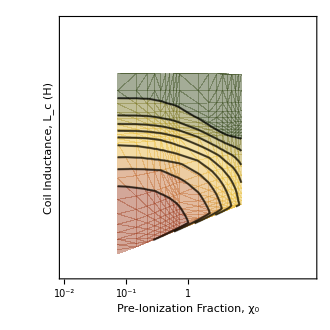

```mathematica
X=Table[Log[10,ΠionT[[j]]],{j,1,Nsols}];
Y=Table[Log[10,EionT[[j]]],{j,1,Nsols}];
Z=Table[ηmT[[j]],{j,1,Nsols}];


LogLogContourPlot[X,Y,Z,"Pre-Ionization Fraction, χ_0","Coil Inductance, L_c (H)",-2,2,-2,2]
```

Thesis Plots 02-16-2022

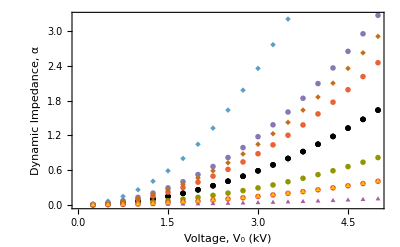

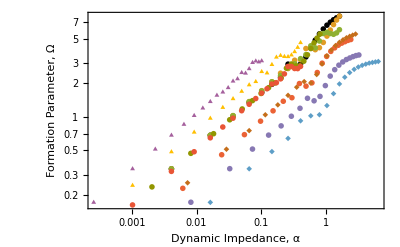

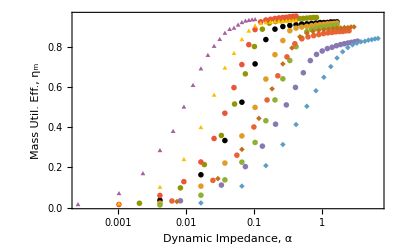

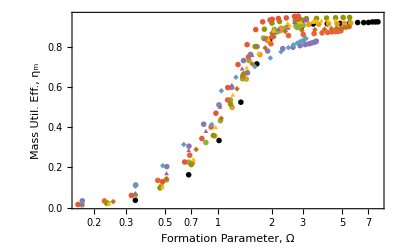

```mathematica
αT = Table[(LcT[[j]] C0T[[j]]^2 V0T[[j]]^2)/(mbitT[[j]] zcT[[j]]^2),{j,1,Nsols}];
P1T=0.005*Sqrt[(2*10^-6)/(5*10^-8)];
P2T = Table[Rp[LcT[[j]],C0T[[j]],nn0T[[j]] ,nn0T[[j]],Te0T[[j]],ws0T[[j]],routT[[j]],rinT[[j]]]*Sqrt[C0T[[j]]/L0T[[j]]],{j,1,Nsols}];


V0T1=MasterTable[[2;;21,17]]; (* Black *)
V0T2=MasterTable[[22;;41,17]]; (* Yellow *)
V0T3=MasterTable[[42;;61,17]]; (* Green *)
V0T4=MasterTable[[62;;81,17]]; (* Red *)
V0T5=MasterTable[[82;;101,17]]; (* Purple *)
V0T6=MasterTable[[102;;121,17]]; (* Cyan *)
V0T7=MasterTable[[122;;141,17]]; (* Brown *)
V0T8=MasterTable[[142;;161,17]]; (* Purple *)
V0T9=MasterTable[[162;;181,17]]; (* Yellow *)
V0T10=MasterTable[[182;;201,17]]; (* Green *)
V0T11=MasterTable[[202;;221,17]]; (* Red *)

MultiCasePlot[X1_,Y1_,X2_,Y2_,X3_,Y3_,X4_,Y4_,X5_,Y5_,X6_,Y6_,X7_,Y7_,X8_,Y8_,X9_,Y9_,X10_,Y10_,X11_,Y11_,xlabel_,ylabel_]:=Show[
ListPlot[
{Table[{X1[[ii]],Y1[[ii]]},{ii,1,20}],
Table[{X2[[ii]],Y2[[ii]]},{ii,1,20}],
Table[{X3[[ii]],Y3[[ii]]},{ii,1,20}],
Table[{X4[[ii]],Y4[[ii]]},{ii,1,20}],
Table[{X5[[ii]],Y5[[ii]]},{ii,1,20}],
Table[{X6[[ii]],Y6[[ii]]},{ii,1,20}],
Table[{X7[[ii]],Y7[[ii]]},{ii,1,20}],
Table[{X8[[ii]],Y8[[ii]]},{ii,1,20}],
Table[{X9[[ii]],Y9[[ii]]},{ii,1,20}],
Table[{X10[[ii]],Y10[[ii]]},{ii,1,20}],
Table[{X11[[ii]],Y11[[ii]]},{ii,1,20}]},
Joined->False,PlotStyle->{Black,Black,Black,ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[5]],ColorData[97,"ColorList"][[7]],ColorData[97,"ColorList"][[6]],ColorData[97,"ColorList"][[9]],ColorData[97,"ColorList"][[8]],ColorData[97,"ColorList"][[10]],ColorData[97,"ColorList"][[11]]},PlotMarkers->{{•,20},{•,8},{•,8},{◼,8},{◼,8},{◆,8},{◆,8},{▲,8},{▲,8},{▮,8},{▮,8}}],
Frame->True,
ImageSize->400,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

MultiLogPlot[X1_,Y1_,X2_,Y2_,X3_,Y3_,X4_,Y4_,X5_,Y5_,X6_,Y6_,X7_,Y7_,X8_,Y8_,X9_,Y9_,X10_,Y10_,X11_,Y11_,xlabel_,ylabel_]:=Show[
ListLogLogPlot[
{Table[{X1[[ii]],Y1[[ii]]},{ii,1,20}],
Table[{X2[[ii]],Y2[[ii]]},{ii,1,20}],
Table[{X3[[ii]],Y3[[ii]]},{ii,1,20}],
Table[{X4[[ii]],Y4[[ii]]},{ii,1,20}],
Table[{X5[[ii]],Y5[[ii]]},{ii,1,20}],
Table[{X6[[ii]],Y6[[ii]]},{ii,1,20}],
Table[{X7[[ii]],Y7[[ii]]},{ii,1,20}],
Table[{X8[[ii]],Y8[[ii]]},{ii,1,20}],
Table[{X9[[ii]],Y9[[ii]]},{ii,1,20}],
Table[{X10[[ii]],Y10[[ii]]},{ii,1,20}],
Table[{X11[[ii]],Y11[[ii]]},{ii,1,20}]},
Joined->False,PlotStyle->{Black,ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[5]],ColorData[97,"ColorList"][[7]],ColorData[97,"ColorList"][[6]],ColorData[97,"ColorList"][[9]],ColorData[97,"ColorList"][[8]],ColorData[97,"ColorList"][[10]],ColorData[97,"ColorList"][[11]]},PlotMarkers->{{•,20},{•,8},{•,8},{◼,8},{◼,8},{◆,8},{◆,8},{▲,8},{▲,8},{▮,8},{▮,8}}],
Frame->True,
PlotRange->{Automatic,Automatic},
ImageSize->400,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

MultiLogLinePlot[X1_,Y1_,X2_,Y2_,X3_,Y3_,X4_,Y4_,X5_,Y5_,X6_,Y6_,X7_,Y7_,X8_,Y8_,X9_,Y9_,X10_,Y10_,X11_,Y11_,xlabel_,ylabel_]:=Show[
ListLogLinearPlot[
{Table[{X1[[ii]],Y1[[ii]]},{ii,1,20}],
Table[{X2[[ii]],Y2[[ii]]},{ii,1,20}],
Table[{X3[[ii]],Y3[[ii]]},{ii,1,20}],
Table[{X4[[ii]],Y4[[ii]]},{ii,1,20}],
Table[{X5[[ii]],Y5[[ii]]},{ii,1,20}],
Table[{X6[[ii]],Y6[[ii]]},{ii,1,20}],
Table[{X7[[ii]],Y7[[ii]]},{ii,1,20}],
Table[{X8[[ii]],Y8[[ii]]},{ii,1,20}],
Table[{X9[[ii]],Y9[[ii]]},{ii,1,20}],
Table[{X10[[ii]],Y10[[ii]]},{ii,1,20}],
Table[{X11[[ii]],Y11[[ii]]},{ii,1,20}]},
Joined->False,PlotStyle->{Black,ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[5]],ColorData[97,"ColorList"][[7]],ColorData[97,"ColorList"][[6]],ColorData[97,"ColorList"][[9]],ColorData[97,"ColorList"][[8]],ColorData[97,"ColorList"][[10]],ColorData[97,"ColorList"][[11]]},PlotMarkers->{{•,20},{•,8},{•,8},{◼,8},{◼,8},{◆,8},{◆,8},{▲,8},{▲,8},{▮,8},{▮,8}}
],
Frame->True,
PlotRange->{Automatic,Automatic},
ImageSize->400,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

MultiCasePlot[V0T1/1000,αT[[1;;20]],V0T2/1000,αT[[21;;40]],V0T3/1000,αT[[41;;60]],V0T4/1000,αT[[61;;80]],V0T5/1000,αT[[81;;100]],V0T6/1000,αT[[101;;120]],V0T7/1000,αT[[121;;140]],V0T8/1000,αT[[141;;160]],V0T9/1000,αT[[161;;180]],V0T10/1000,αT[[181;;200]],V0T11/1000,αT[[201;;220]],"Voltage, V_0 (kV)","Dynamic Impedance, α"]


MultiLogPlot[αT[[1;;20]],EionT[[1;;20]],αT[[21;;40]],EionT[[21;;40]],αT[[41;;60]],EionT[[41;;60]],αT[[61;;80]],EionT[[61;;80]],αT[[81;;100]],EionT[[81;;100]],αT[[101;;120]],EionT[[101;;120]],αT[[121;;140]],EionT[[121;;140]],αT[[141;;160]],EionT[[141;;160]],αT[[161;;180]],EionT[[161;;180]],αT[[181;;200]],EionT[[181;;200]],αT[[201;;220]],EionT[[201;;220]],"Dynamic Impedance, α","Formation Parameter, Ω"]


MultiLogLinePlot[αT[[1;;20]],ηmT[[1;;20]],αT[[21;;40]],ηmT[[21;;40]],αT[[41;;60]],ηmT[[41;;60]],αT[[61;;80]],ηmT[[61;;80]],αT[[81;;100]],ηmT[[81;;100]],αT[[101;;120]],ηmT[[101;;120]],αT[[121;;140]],ηmT[[121;;140]],αT[[141;;160]],ηmT[[141;;160]],αT[[161;;180]],ηmT[[161;;180]],αT[[181;;200]],ηmT[[181;;200]],αT[[201;;220]],ηmT[[201;;220]],"Dynamic Impedance, α","Mass Util. Eff., η_m"]


MultiLogLinePlot[EionT[[1;;20]],ηmT[[1;;20]],0.7EionT[[21;;40]],ηmT[[21;;40]],0.5EionT[[41;;60]],ηmT[[41;;60]],EionT[[61;;80]],ηmT[[61;;80]],EionT[[81;;100]],ηmT[[81;;100]],EionT[[101;;120]],ηmT[[101;;120]],EionT[[121;;140]],ηmT[[121;;140]],EionT[[141;;160]],ηmT[[141;;160]],EionT[[161;;180]],ηmT[[161;;180]],EionT[[181;;200]],ηmT[[181;;200]],EionT[[201;;220]],ηmT[[201;;220]],"Formation Parameter, Ω","Mass Util. Eff., η_m"]
```

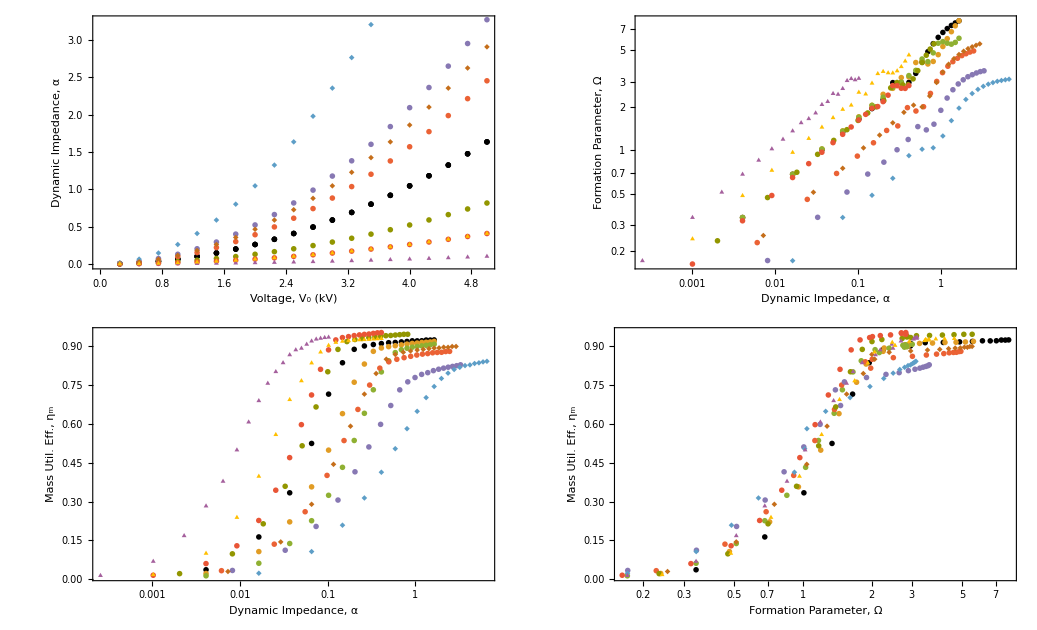

```mathematica
Print[GraphicsGrid[{
{MultiCasePlot[V0T1/1000,αT[[1;;20]],V0T2/1000,αT[[21;;40]],V0T3/1000,αT[[41;;60]],V0T4/1000,αT[[61;;80]],V0T5/1000,αT[[81;;100]],V0T6/1000,αT[[101;;120]],V0T7/1000,αT[[121;;140]],V0T8/1000,αT[[141;;160]],V0T9/1000,αT[[161;;180]],V0T10/1000,αT[[181;;200]],V0T11/1000,αT[[201;;220]],"Voltage, V_0 (kV)","Dynamic Impedance, α"],MultiLogPlot[αT[[1;;20]],EionT[[1;;20]],αT[[21;;40]],EionT[[21;;40]],αT[[41;;60]],EionT[[41;;60]],αT[[61;;80]],EionT[[61;;80]],αT[[81;;100]],EionT[[81;;100]],αT[[101;;120]],EionT[[101;;120]],αT[[121;;140]],EionT[[121;;140]],αT[[141;;160]],EionT[[141;;160]],αT[[161;;180]],EionT[[161;;180]],αT[[181;;200]],EionT[[181;;200]],αT[[201;;220]],EionT[[201;;220]],"Dynamic Impedance, α","Formation Parameter, Ω"]},
{MultiLogLinePlot[αT[[1;;20]],ηmT[[1;;20]],αT[[21;;40]],ηmT[[21;;40]],αT[[41;;60]],ηmT[[41;;60]],αT[[61;;80]],ηmT[[61;;80]],αT[[81;;100]],ηmT[[81;;100]],αT[[101;;120]],ηmT[[101;;120]],αT[[121;;140]],ηmT[[121;;140]],αT[[141;;160]],ηmT[[141;;160]],αT[[161;;180]],ηmT[[161;;180]],αT[[181;;200]],ηmT[[181;;200]],αT[[201;;220]],ηmT[[201;;220]],"Dynamic Impedance, α","Mass Util. Eff., η_m"],MultiLogLinePlot[EionT[[1;;20]],ηmT[[1;;20]],0.7EionT[[21;;40]],ηmT[[21;;40]],0.5EionT[[41;;60]],ηmT[[41;;60]],EionT[[61;;80]],ηmT[[61;;80]],EionT[[81;;100]],ηmT[[81;;100]],EionT[[101;;120]],ηmT[[101;;120]],EionT[[121;;140]],ηmT[[121;;140]],EionT[[141;;160]],ηmT[[141;;160]],EionT[[161;;180]],ηmT[[161;;180]],EionT[[181;;200]],ηmT[[181;;200]],EionT[[201;;220]],ηmT[[201;;220]],"Formation Parameter, Ω","Mass Util. Eff., η_m"]}}
,Spacings-> {5,-5},ImageSize-> 800]];
```

Thesis Plots 02-23-2022

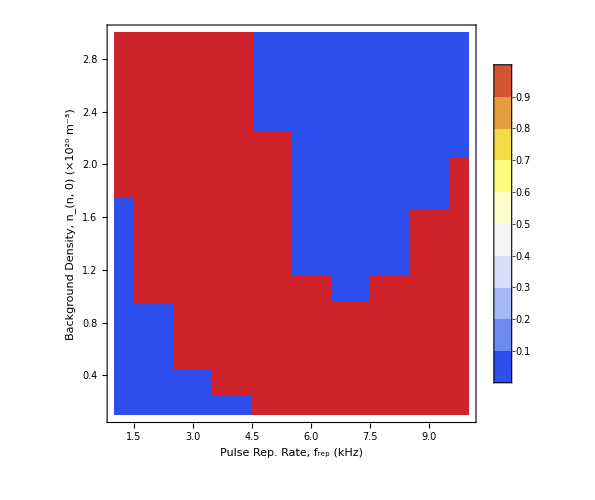

```mathematica
(** Evaluate this to load csv file data **)
MasterTable=Import[DataIOFile[[1]]];
Nsols=Dimensions[MasterTable][[1]]-1;

(** Generate Tables of Data from MasterTable **)

zmaxT=MasterTable[[2;;Nsols+1,1]];
zstepsT=MasterTable[[2;;Nsols+1,2]];
tmaxT=MasterTable[[2;;Nsols+1,3]];
tstepsT=MasterTable[[2;;Nsols+1,4]];
zs0T=MasterTable[[2;;Nsols+1,5]];
ws0T=MasterTable[[2;;Nsols+1,6]];
nn0T=MasterTable[[2;;Nsols+1,7]];
χi0T=MasterTable[[2;;Nsols+1,8]];
zχiT=MasterTable[[2;;Nsols+1,9]];
Te0T=MasterTable[[2;;Nsols+1,10]];
Ti0T=MasterTable[[2;;Nsols+1,11]];
znT=MasterTable[[2;;Nsols+1,12]];
LcT=MasterTable[[2;;Nsols+1,13]];
L0T=MasterTable[[2;;Nsols+1,14]];
RcT=MasterTable[[2;;Nsols+1,15]];
C0T=MasterTable[[2;;Nsols+1,16]];
V0T=MasterTable[[2;;Nsols+1,17]];
zcT=MasterTable[[2;;Nsols+1,18]];
routT=MasterTable[[2;;Nsols+1,19]];
rinT=MasterTable[[2;;Nsols+1,20]];
zc0T=MasterTable[[2;;Nsols+1,21]];
frepT=MasterTable[[2;;Nsols+1,22]];
NpT=MasterTable[[2;;Nsols+1,23]];
SSBool=MasterTable[[2;;Nsols+1,24]];
ηRT=MasterTable[[2;;Nsols+1,25]];
ηmT=MasterTable[[2;;Nsols+1,26]];

SSData = Table[{frepT[[j]]/1000,nn0T[[j]]/10^20,SSBool[[j]]},{j,1,Nsols}];
nRData =Table[{frepT[[j]]/1000,nn0T[[j]]/10^20,ηRT[[j]]},{j,1,Nsols}];
nmData =Table[{frepT[[j]]/1000,nn0T[[j]]/10^20,ηmT[[j]]},{j,1,Nsols}];

MassFlowPlot[Data_,xlabel_,ylabel_]:=
Show[{
ListContourPlot[Data,PlotRange->Full,PlotLegends->Automatic,Mesh-> None,ColorFunction->"TemperatureMap",InterpolationOrder->0]},
Frame->True,
AspectRatio->1,
ImageSize->500,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

EffContourPlot[Data_,xlabel_,ylabel_]:=
Show[{
ListContourPlot[Data,PlotRange->Full,ContourLabels->All,Mesh-> None,ColorFunction->({Opacity[0.5],ColorData["SandyTerrain"][#]}&)]},
Frame->True,
AspectRatio->1,
ImageSize->500,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

MassFlowPlot[SSData,"Pulse Rep. Rate, f_rep (kHz)","Background   Density, n_(n, 0) (×10^20 m^-3)"] 
EffContourPlot[nRData,"Pulse Rep. Rate, f_rep (kHz)","Background   Density, n_(n, 0) (×10^20 m^-3)"] 
EffContourPlot[nmData,"Pulse Rep. Rate, f_rep (kHz)","Background   Density, n_(n, 0) (×10^20 m^-3)"]
```

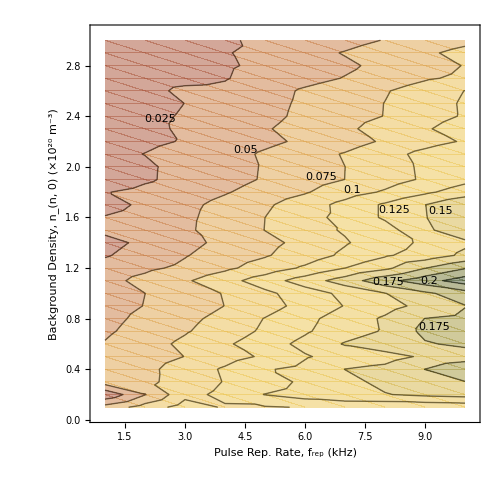

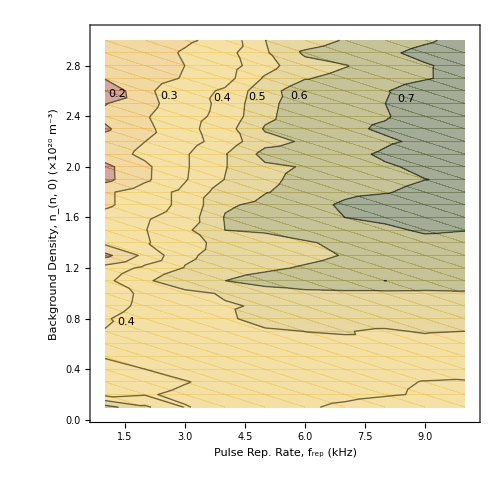

Thesis Plots 02-25-2022

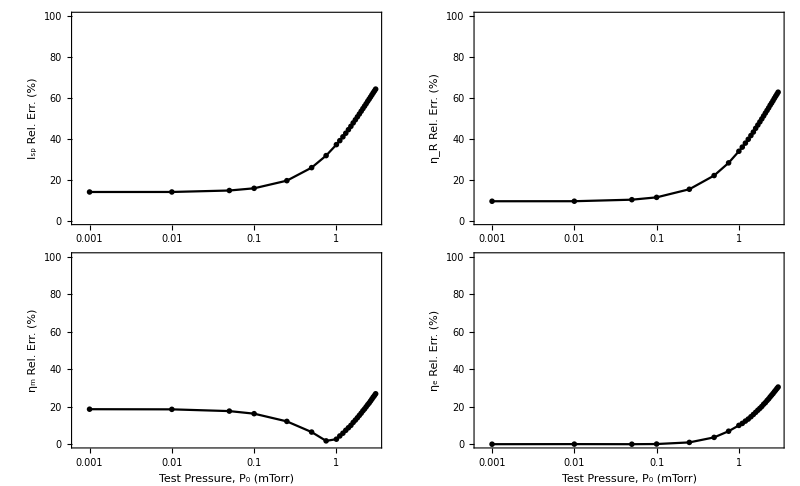

```mathematica
(** Evaluate this to load csv file data **)
MasterTable=Import[DataIOFile[[1]]];
Nsols=Dimensions[MasterTable][[1]]-1;

(** Generate Tables of Data from MasterTable **)

zmaxT=MasterTable[[2;;Nsols+1,1]];
zstepsT=MasterTable[[2;;Nsols+1,2]];
tmaxT=MasterTable[[2;;Nsols+1,3]];
tstepsT=MasterTable[[2;;Nsols+1,4]];
zs0T=MasterTable[[2;;Nsols+1,5]];
ws0T=MasterTable[[2;;Nsols+1,6]];
nn0T=MasterTable[[2;;Nsols+1,7]];
χi0T=MasterTable[[2;;Nsols+1,8]];
zχiT=MasterTable[[2;;Nsols+1,9]];
Te0T=MasterTable[[2;;Nsols+1,10]];
Ti0T=MasterTable[[2;;Nsols+1,11]];
znT=MasterTable[[2;;Nsols+1,12]];
LcT=MasterTable[[2;;Nsols+1,13]];
L0T=MasterTable[[2;;Nsols+1,14]];
RcT=MasterTable[[2;;Nsols+1,15]];
C0T=MasterTable[[2;;Nsols+1,16]];
V0T=MasterTable[[2;;Nsols+1,17]];
zcT=MasterTable[[2;;Nsols+1,18]];
routT=MasterTable[[2;;Nsols+1,19]];
rinT=MasterTable[[2;;Nsols+1,20]];
zc0T=MasterTable[[2;;Nsols+1,21]];
frepT=MasterTable[[2;;Nsols+1,22]];
NpT=MasterTable[[2;;Nsols+1,23]];
PtestT=MasterTable[[2;;Nsols+1,24]];
vsT=MasterTable[[2;;Nsols+1,25]];
wsT=MasterTable[[2;;Nsols+1,26]];
nsT=MasterTable[[2;;Nsols+1,27]];
IbitT=MasterTable[[2;;Nsols+1,28]];
IspT=MasterTable[[2;;Nsols+1,29]];
ηTT=MasterTable[[2;;Nsols+1,30]];
ηRT=MasterTable[[2;;Nsols+1,31]];
ηmT=MasterTable[[2;;Nsols+1,32]];
ηeT=MasterTable[[2;;Nsols+1,33]];

Prange=PtestT[[1;;28]];
Eisp=Abs[IspT[[1;;28]]-IspT[[29]]]/IspT[[29]]*100;
EnR=Abs[ηRT[[1;;28]]-ηRT[[29]]]/ηRT[[29]]*100;
Enm=Abs[ηmT[[1;;28]]-ηmT[[29]]]/ηmT[[29]]*100;
Ene=Abs[ηeT[[1;;28]]-ηeT[[29]]]/ηeT[[29]]*100;

BFErrPlot[Ytable_,xlabel_,ylabel_]:=Show[{ListLogLinearPlot[Table[{Prange[[ii]]*10^3,Ytable[[ii]]},{ii,1,28}],Joined->True,PlotMarkers->{▪},PlotStyle-> Black,PlotRange->{Automatic,{0,100}}]},
Frame->True,
ImageSize->400,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

(* BFErrPlot[Eisp,"I_sp Rel. Err. (%)"];
BFErrPlot[EnR,"η_R Rel. Err. (%)"];
BFErrPlot[Enm,"η_m Rel. Err. (%)"];
BFErrPlot[Ene,"η_e Rel. Err. (%)"]; *)

Print[GraphicsGrid[{
{BFErrPlot[Eisp,"","I_sp Rel. Err. (%)"],BFErrPlot[EnR,"","η_R Rel. Err. (%)"]},
{BFErrPlot[Enm,"Test Pressure, P_0 (mTorr)","η_m Rel. Err. (%)"],BFErrPlot[Ene,"Test Pressure, P_0 (mTorr)","η_e Rel. Err. (%)"]}}
,Spacings-> {5,-5},ImageSize-> 800]];
```